```mathematica
DSolve[{
theta''[t]==A*Cos[alpha]*Cos[phi[t]-omega*t]+phi'[t]*phi'[t]*Sin[2*alpha]/2-B*phi'[t]*Sin[alpha],
phi''[t]*Sin[alpha]==-A*Sin[phi[t]-omega*t]}
	,{theta[t], phi[t]},t]
```

```mathematica
DSolve[{
	phi''[t]*Sin[alpha]==-A*Sin[phi[t]-omega*t]},{phi[t]},t]
```

```mathematica
DSolve[
	0==Cos[Pi/6]*Cos[phi[t]-t]+phi'[t]*phi'[t]*Sin[Pi/3]/2-phi'[t]*Sin[Pi/6]
	,{phi[t]},t]
```

```mathematica
Solve[Cos[alpha]+omega^2 *Sin[alpha]*Cos[alpha]-omega*Sin[alpha]==0,alpha]
```

```mathematica
alpha[omega_]:=Values[Solve[Cos[x]+omega^2 *Sin[x]*Cos[x]-omega*Sin[x]==0,x,Assumptions->{0<x<Pi}]]
```

```mathematica
N[alpha[2]]
```

{{1.16678}}

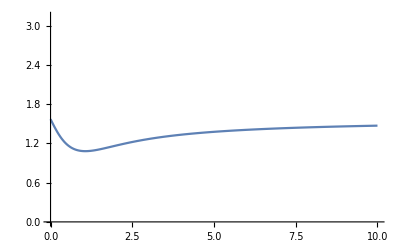

```mathematica
Plot[alpha[omega],{omega,0,10}, PlotRange->{0,Pi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

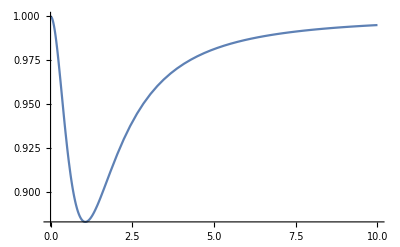

```mathematica
Plot[Sin[alpha[omega]],{omega, 0, 10}]
```

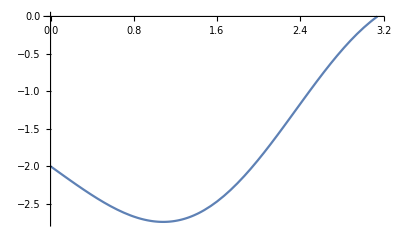

```mathematica
Plot[-Sin[x]-1-Cos[x]-Sin[x]*Sin[x]/2,{x,0,Pi}]
```

```mathematica
DynamicModule[{a},Column[{Dynamic@Plot[-Cos[a]*Sin[x]-1-Cos[x]-Sin[x]*Sin[x]/2,{x,0,Pi}],Slider[Dynamic@a,{0,10}]}]]
```

```mathematica
DSolve[{
theta''[t]==Cos[theta[t]]+Sin[theta[t]]*Cos[theta[t]]-Sin[theta[t]],
theta[0]==0,
theta'[0]==0
},theta[t],t]
```